```mathematica
ClearAll[vel,gap]
```

```mathematica
Do[
Do[
dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
vel[l][d][1]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/VelLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-1.txt",{Number,Number,Number}];
vel[l][d][2]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/VelLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-2.txt",{Number,Number,Number}];
vel[l][d][3]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/VelLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-3.txt",{Number,Number,Number}];
gap[l][d][1]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/GapLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-1.txt",{Number,Number,Number}];
gap[l][d][2]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/GapLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-2.txt",{Number,Number,Number}];
gap[l][d][3]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/GapLabelTime-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-3.txt",{Number,Number,Number}];
,{l,{5,10,30}}]
,{d,{0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.0805,0.0815,0.0825,0.0835,0.0845,0.0855,0.0865,0.0875,0.0885,0.0895,0.0905,0.0915,0.0925,0.0935,0.0945}}]
```

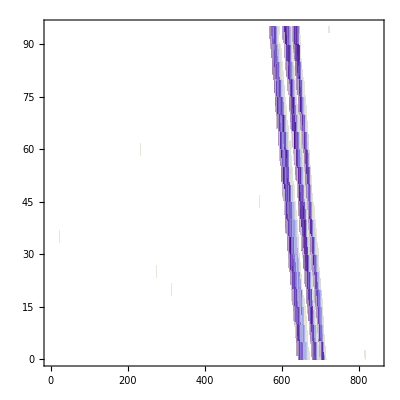

```mathematica
ListDensityPlot[vel[0.085][1],PlotRange->{Full,Full,{0,7}}]
```

```mathematica
l=30;
d=0.083;
i=3;
ListPlot3D[vel[l][d][i],PlotRange->{Full,Full,{0,9}}]

ListPlot3D[gap[l][d][i],PlotRange->{Full,Full,{0,8}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

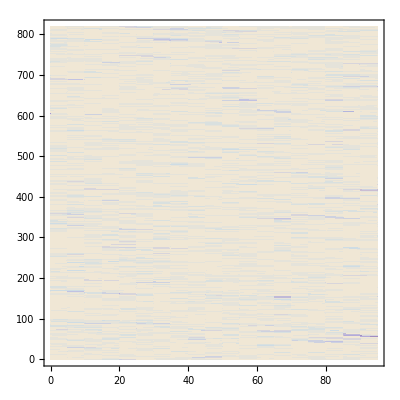

```mathematica
ListDensityPlot[vel]
```

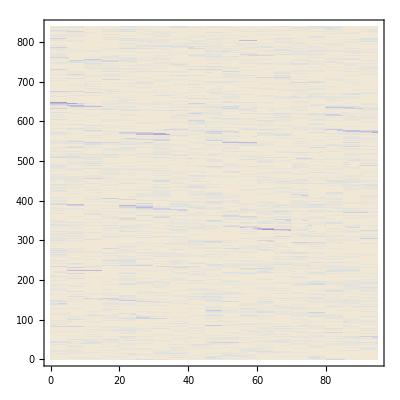

```mathematica
ListDensityPlot[vel]
```

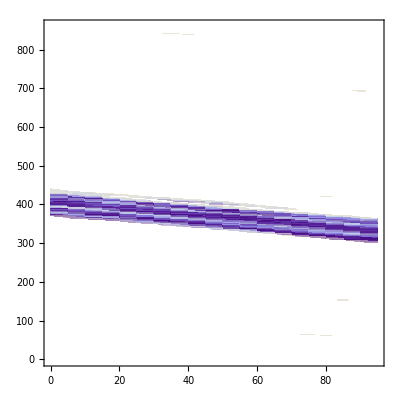

```mathematica
ListDensityPlot[vel,PlotRange->{Full,Full,{0,7}}]
```

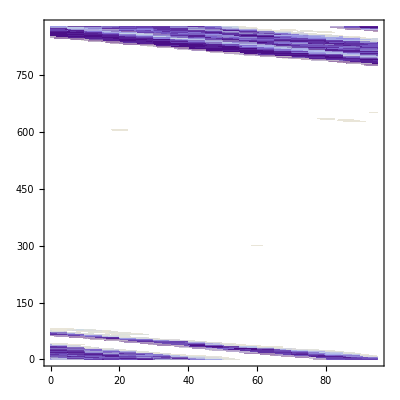

```mathematica
ListDensityPlot[vel,PlotRange->{Full,Full,{0,7}}]
```

```mathematica
vel=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/check.txt",{Number,Number}];
vel2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/check2.txt",{Number,Number}];
```

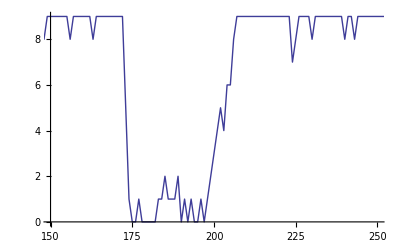

```mathematica
ListLinePlot[vel,PlotRange->{{150,250},All}]
```

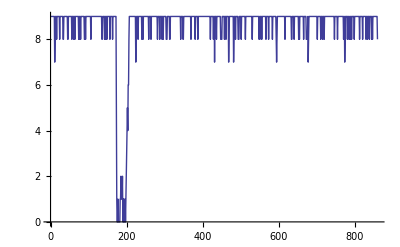

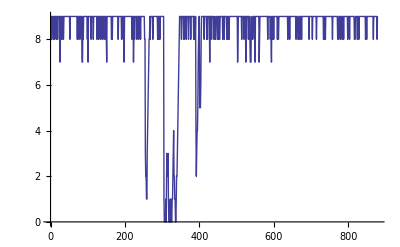

```mathematica
ListLinePlot[vel]
ListLinePlot[vel2,PlotRange->Full]
```

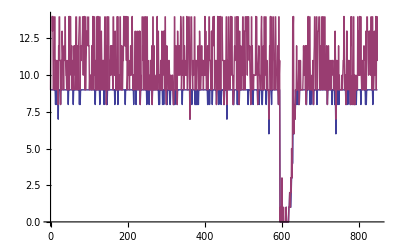

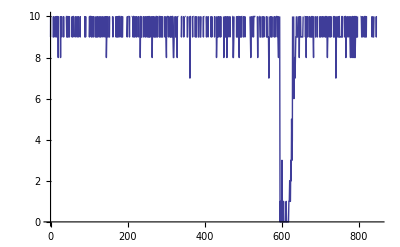

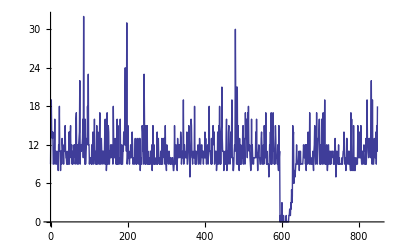

```mathematica
t=60;
i=1;
l=10;
d=0.085;
auxv=Select[vel[l][d][i],#[[2]]==t &];
auxg=Select[gap[l][d][i],#[[2]]==t &];
veltime[l][d][i][t]=Table[{auxv[[All,1]][[i]],auxv[[All,3]][[i]]},{i,1,Length[auxv]}];
gaptime[l][d][i][t]=Table[{auxg[[All,1]][[i]],auxg[[All,3]][[i]]},{i,1,Length[auxg]}];
ListLinePlot[{veltime[l][d][i][t],gaptime[l][d][i][t]},PlotRange->PlotRange->{Full,{0,10}}]
ListLinePlot[gaptime[l][d][i][t],PlotRange->{Full,{0,10}}]
ListLinePlot[gaptime[l][d][i][t],PlotRange->Full]
```

```mathematica
Do[
Do[
dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
jaml[l][d]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/JamLengthTimeEvo-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-1.txt",{Number,Number}];

jamn[l][d]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/NumCarsInJamTimeEvo-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-1.txt",{Number,Number}];

,{d,{0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.0805,0.0815,0.0825,0.0835,0.0845,0.0855,0.0865,0.0875,0.0885,0.0895,0.0905,0.0915,0.0925,0.0935,0.0945}}];

JAM[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/JamLengthAv-l"<>ll<>"k-v9-p0.1-1.txt",{Number,Number}];

NUM[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/NumCarsInJamAv-l"<>ll<>"k-v9-p0.1-1.txt",{Number,Number}];

,{l,{5,10,30}}]
```

```mathematica
Do[
Do[
dd=ToString[d];
ll=ToString[l];
v="9";
p="0.1";
jaml[l][d]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/JamLengthTimeEvo-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-2.txt",{Number,Number}];

jamn[l][d]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/NumCarsInJamTimeEvo-l"<>ll<>"k-v9-p0.1-d"<>dd<>"-2.txt",{Number,Number}];

,{d,{0.082,0.0821,0.0822,0.0823,0.0824,0.0825,0.0826,0.0827,0.0828,0.0829,0.083,0.0831,0.0832,0.0833,0.0834,0.0835,0.0836,0.0837,0.0838,0.0839,0.084,0.0841,0.0842,0.0843,0.0844,0.0845,0.0846,0.0847,0.0848,0.0849,0.085,0.0851,0.0852,0.0853,0.0854,0.0855,0.0856,0.0857,0.0858,0.0859}}];

JAM2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/JamLengthAv-l"<>ll<>"k-v9-p0.1-2.txt",{Number,Number}];

NUM2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/NumCarsInJamAv-l"<>ll<>"k-v9-p0.1-2.txt",{Number,Number}];

,{l,{5,10,30}}]
```

```mathematica
Do[
JAM[l]=Append[JAM[l],JAM2[l]];
NUM[l]=Append[NUM[l],NUM2[l]];
,{l,{5,10,30}}]
```

```mathematica
Do[
JAMs[l]=Table[{JAM[l][[All,1]][[i]],JAM[l][[All,2]][[i]]/(l*1000)},{i,1,Length[JAM[l]]}];
NUMs[l]=Table[{NUM[l][[All,1]][[i]],NUM[l][[All,2]][[i]]/(l*1000)},{i,1,Length[NUM[l]]}];
,{l,{5,10,30}}]
```

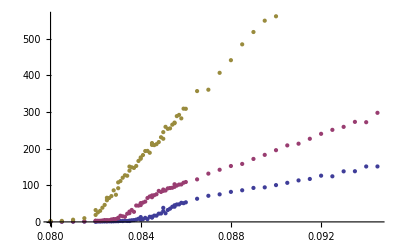

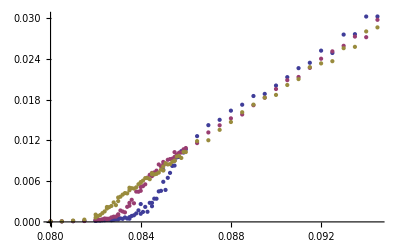

```mathematica
ListPlot[{JAM[5],JAM[10],JAM[30]}]
ListPlot[{JAMs[5],JAMs[10],JAMs[30]}]
```

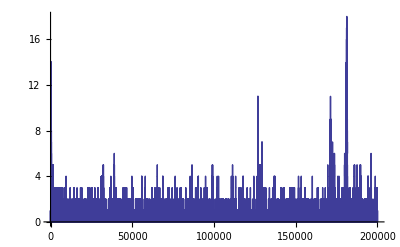

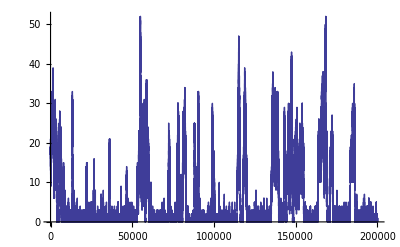

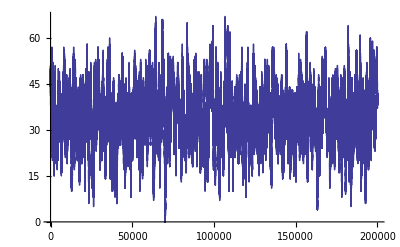

```mathematica
l=5;
d1=0.082;
d2=0.084;
d3=0.087;
ListLinePlot[jamn[l][d1],PlotRange->Full]
ListLinePlot[jamn[l][d2],PlotRange->Full]
ListLinePlot[jamn[l][d3],PlotRange->Full]
```

```mathematica
l1=5;
l2=10;
l3=30;
d=0.083;
ListLinePlot[jamn[l1][d],PlotRange->Full]
ListLinePlot[jamn[l2][d],PlotRange->Full]
ListLinePlot[jamn[l3][d],PlotRange->Full]
ListLinePlot[jaml[l1][d],PlotRange->Full]
ListLinePlot[jaml[l2][d],PlotRange->Full]
ListLinePlot[jaml[l3][d],PlotRange->Full]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»